-Graphics-

# Useful Functions

## WL Training II (Programmers)

Slack channel   #wl-train-prog

-Graphics-

## Learning Objectives

Pure functions

Counting/Grouping

Iterations

Throw/Catch

Levels

Pattern Matching

Cases/Flatten

Replace/ReplaceAll

Condition

## Note

In Wolfram Language one should think in terms of declarative programming, not imperative:
you tell the computer what result you wish to obtain, not how to do it - and let the machine decide the best way.

## Pure functions

```mathematica
Function[x,x/3][9]
```

3

```mathematica
Function[{x,y},x/y][1,4]
```

1/4

```mathematica
cube[x_]:=x^3
```

1

```mathematica
#1/#2&[2,3]
```

2/3

```mathematica
{#1*10,##2}&[1,3,3,3]
```

{10,3,3,3}

```mathematica
({1,2,3}+{1,2,3})^2
```

{4,16,36}

```mathematica
FullForm[#0]&[1]
```

Function[FullForm[Slot[0]]]

```mathematica
{ToUpperCase[#name],ToLowerCase[#city]}&@<|"name"->"Dariia","city"->"Kyiv"|>
```

{DARIIA,kyiv}

### Practice

Use Range and a pure function to create a list of the first 20 squares.
Expected output:

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
#^2&/@Range[20]
```

```mathematica
#^2&@Range[20]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
Attributes[Power]
```

{Listable,NumericFunction,OneIdentity,Protected}

Obtain values from the list above that are larger than 100.
Expected output:

```mathematica
{121,144,169,196,225,256,289,324,361,400}
```

{121,144,169,196,225,256,289,324,361,400}

```mathematica
Select[%35,#>100&]
```

{121,144,169,196,225,256,289,324,361,400}

## Counting/Grouping

GroupBy gives an association that groups the into lists associated with distinct keys.

```mathematica
GroupBy[{{a,b},{a,c},{b,c}},First]
```

<|a→{{a,b},{a,c}},b→{{b,c}}|>

```mathematica
GroupBy[RandomInteger[10,{10000,2}],First]//RepeatedTiming
```

{0.00059,<|0→{{0,6},{0,6},{0,6},{0,1},{0,2},{0,8},{0,4},{0,2},{0,8},{0,5},912,{0,10},{0,10},{0,6},{0,9},{0,9},{0,9},{0,8},{0,0},{0,7},{0,7}},9,1→{1}|>}
 |  |  |  |

```mathematica
GroupBy[{"aa","bc","aaa","aab","abcd","abcde"}, StringLength]
```

<|2→{aa,bc},3→{aaa,aab},4→{abcd},5→{abcde}|>

Tally lists all distinct elements together with their multiplicities.

```mathematica
Tally[{{a,b},{w,x,y,z},E,{w,x,y,z},E},Head[#1]===Head[#2]&]
```

{{{a,b},3},{ⅇ,2}}

```mathematica
Tally[{"aa","bc","aaa","aab","abcd","abcde"}, StringLength]
```

{{1,1},{2,1},{3,4}}

```mathematica
Tally[{a,a,b,a,c,b,a}]
```

{{a,4},{b,2},{c,1}}

Counts does a similar thing but returns an Association.

```mathematica
Counts[{a,a,b,a,c,b,a}]
```

<|a→4,b→2,c→1|>

CountsBy counts values of a list based on values of a given function:

```mathematica
CountsBy[RandomInteger[1000,100],Mod[#,10]&]
```

```mathematica
KeySort@<|0->12,2->13,8->8,6->11,5->8,4->8,9->14,7->7,1->8,3->11|>
```

<|0→12,1→8,2→13,3→11,4→8,5→8,6→11,7→7,8→8,9→14|>

```mathematica
CountsBy[PrimeQ] [RandomInteger[1000,100]]
```

<|False→81,True→19|>

GatherBy gathers elements based on values of a given function:

```mathematica
GatherBy[{1,2,3,4,5},OddQ]
```

{{1,3,5},{2,4}}

```mathematica
GatherBy[Range[1000],Mod[#,10]&]
```

SplitBy splits a list based on successive runs of values of a given function:

```mathematica
SplitBy[{1,11,2,3,12},# ≤ 10 &]
```

{{1},{11},{2,3},{12}}

### Practice

Gather elements of a list of first 20 squares based on their last digit.
Expected output:

{{1,81,121,361},{4,64,144,324},{9,49,169,289},{16,36,196,256},{25,225},{100,400}}

```mathematica
GatherBy[Range[20]^2,Last[IntegerDigits[#]]&]
```

```mathematica
GatherBy[Range[20]^2,Mod[#,10]&]
```

{{1,81,121,361},{4,64,144,324},{9,49,169,289},{16,36,196,256},{25,225},{100,400}}

Get a random sample of 500 words for WordList[] and count how many of them have certain length, and plot the length distribution.
Example output:

```mathematica
list=WordList[];
```

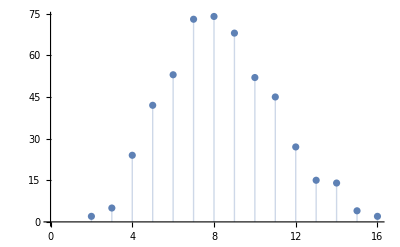

```mathematica
ListPlot[CountsBy[RandomSample[list,500],StringLength],Filling->Axis]
```

## Iterations

Map is an important tool when you need to apply some function to particular parts of an expression. It’s often used with Lists:

```mathematica
Map[f, {1,2, 3,4}]
```

{f[1],f[2],f[3],f[4]}

But it also works on any Head:

```mathematica
a+b+c+d//FullForm
```

Plus[a,b,c,d]

```mathematica
Map[f,a+b+c+d]
```

f[a]+f[b]+f[c]+f[d]

```mathematica
Map[f, {1+2,{ 3+4}},{2}]
```

{3,{f[7]}}

```mathematica
Map[f, anysymbol[1+2, 3+4]]
```

anysymbol[f[3],f[7]]

Specify the level on which to apply f:

```mathematica
Map[f, {{1,2},{ 3,4}},2]
```

{f[{f[1],f[2]}],f[{f[3],f[4]}]}

Shortcut:

```mathematica
f/@Range[10]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

Use Map with pure functions:

```mathematica
list = Range[10000];
```

```mathematica
#^3&/@list;//RepeatedTiming
```

{0.000372,Null}

```mathematica
#^3&[list];//RepeatedTiming
```

{0.00014,Null}

```mathematica
For[i=1,i≤Length[list],i++,list[[i]]^3]//RepeatedTiming
```

{0.0153,Null}

```mathematica
Do[list[[i]]^3,{i,10000}]//RepeatedTiming
```

{0.008,Null}

Perform Map, while also taking index into account:

```mathematica
First[{1}]
```

1

```mathematica
MapIndexed[(Print[#2];#1 * First[#2]) &, {a, b, c}]
```

{1}

{2}

{3}

{a,2 b,3 c}

Scan is useful to produce a side effect.

```mathematica
Scan[Print,{a,b,c}]
```

a

b

c

```mathematica
Scan[Print[#^2]&,{1,2,3}]
```

1

4

9

Scan discards the results of applying the function. Unlike Map, it does not build up a new expression to return.

```mathematica
Scan[Print[# ≥3]&,{1, 2, 3, 4, 5}]
```

False

False

True

True

True

```mathematica
Scan[If[# ≥3, Return[#]] &, {1, 2, 3, 4, 5}]
```

3

```mathematica
SelectFirst[{1, 2, 3, 4, 5},#≥3&]
```

3

### Practice

Use /@ twice to reproduce the result below.

```mathematica
Table[g[f[n]],{n,10}]
```

{g[f[1]],g[f[2]],g[f[3]],g[f[4]],g[f[5]],g[f[6]],g[f[7]],g[f[8]],g[f[9]],g[f[10]]}

```mathematica
g/@f/@Range[10]
```

{g[f[1]],g[f[2]],g[f[3]],g[f[4]],g[f[5]],g[f[6]],g[f[7]],g[f[8]],g[f[9]],g[f[10]]}

```mathematica
f[Range[10]]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
SetAttributes[f,Listable]
```

Given a 10 by 10 matrix of random integers

```mathematica
matrix =RandomInteger[10,{10,10}];
```

use MapIndexed to obtain a structure like this:

{5}
{8,1}
{7,3,8}
{8,4,4,8}
{2,8,0,1,2}
{9,9,8,4,1,10}
{4,3,3,8,2,6,10}
{4,4,6,8,9,6,9,1}
{9,8,8,2,2,0,9,8,0}
{7,3,4,7,6,7,8,10,5,8}

```mathematica
MapIndexed[Take[#1,First[#2]]&,matrix]//Column
```

{8}
{4,2}
{7,4,1}
{8,2,3,6}
{0,0,3,7,4}
{9,8,8,8,3,5}
{3,2,4,10,8,8,7}
{3,10,9,3,6,7,1,2}
{3,7,10,6,6,2,7,5,0}
{4,9,9,2,5,2,1,4,6,1}

```mathematica
MapIndexed[Part[#1,1;;First[#2]]&,matrix]//Column
```

{8}
{4,2}
{7,4,1}
{8,2,3,6}
{0,0,3,7,4}
{9,8,8,8,3,5}
{3,2,4,10,8,8,7}
{3,10,9,3,6,7,1,2}
{3,7,10,6,6,2,7,5,0}
{4,9,9,2,5,2,1,4,6,1}

### Styling

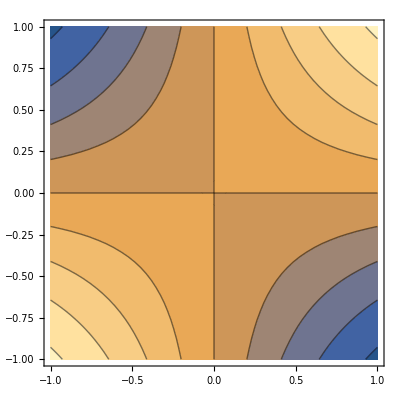

```mathematica
ContourPlot[Sin[x y],{x,-1,1},{y,-1,1}]
```

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
{#,ContourPlot[Sin[x y],{x,-1,1},{y,-1,1}, ColorFunction->#]}&/@ColorData["Gradients"]//Column
```

## Throw/Catch

You can use Throwpaclet:ref/Throw and Catchpaclet:ref/Catch to divert the operation of functional programming constructs, allowing for example the evaluation of such constructs to continue only until some condition has been met. Note that if you stop evaluation using Throwpaclet:ref/Throw, then the structure of the result you get may be quite different from what you would have got if you had allowed the evaluation to complete.

```mathematica
Clear[f]
f[x_] /; x ≤ 0 := Throw[$Failed,"LessThan0"]
f[x_] := x+1
```

```mathematica
f[3]
```

4

```mathematica
f[-4]
```

Throw::nocatch: Uncaught Throw[$Failed,error] returned to top level.

Hold[Throw[$Failed,error]]

```mathematica
g::zero="Less than 0";
```

```mathematica
g[x_]:=Catch[
f[x], 
"LessThan0", 
Message[g::zero];
#&
]
```

```mathematica
g[-3]
```

g::zero: Less than 0

$Failed

```mathematica
NestList[(#^2+1)&,1,10]
```

{1,2,5,26,677,458330,210066388901,44127887745906175987802,1947270476915296449559703445493848930452791205,3791862310265926082868235028027893277370233152247388584761734150717768254410341175325352026,14378219780015246281818710879551167697596193767663736497089725524386087657390556152293078723153293423353330879856663164406809615688082297859526620035327291442156498380795040822304677}

Stop if an iteration gets too large . Now the evaluation of the NestListpaclet:ref/NestList is diverted, and the single number given as the argument of Throwpaclet:ref/Throw is returned:

```mathematica
Catch[NestList[If[#>10000,Throw[#],#^2+1]&,1,10]]
```

458330

Since there is no Throwpaclet:ref/Throw encountered, the result here is just as before:

```mathematica
Catch[NestList[1/(#+1)&,-2.5,6]]
```

{-2.5,-0.666667,3.,0.25,0.8,0.555556,0.642857}

Use Quiet and Check to suppress messages:

```mathematica
Import["path/to/file.txt"]
```

Import::nffil: File path/to/file.txt not found during Import.

$Failed

```mathematica
Quiet @ Check[
Import["path/to/file.txt"], 
1234
]
```

1234

## Reap/Sow

Reap gives the value of an expression together with all expressions to which Sow has been applied during its evaluation :

```mathematica
Reap[Sum[Sow[i^3]+1,{i,10}]]
```

{3035,{{1,8,27,64,125,216,343,512,729,1000}}}

## Levels

```mathematica
data = {{1, 2, 3}, {{4, 5}, {6, 7}}}
```

{{1,2,3},{{4,5},{6,7}}}

Every expression has a Head:

```mathematica
Head[data]
data[[0]]
```

List

List

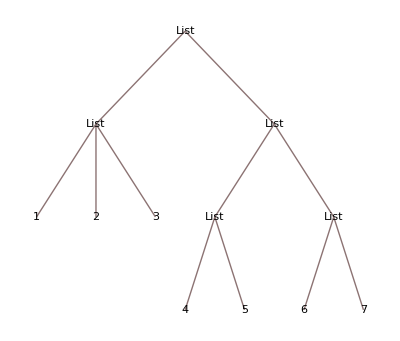

```mathematica
TreeForm[data]
```

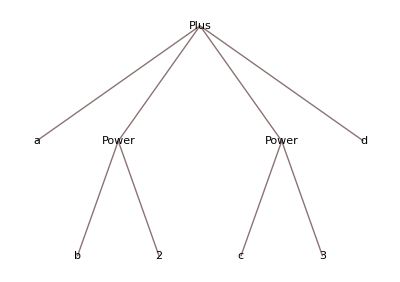

```mathematica
TreeForm[a+b^2+c^3+d]
```

```mathematica
Dimensions[data,4]
```

{2}

```mathematica
Dimensions[{{a,b,c},{d,e,f}}]
```

{2,3}

```mathematica
Level[data,1]
```

{{1,2,3},{{4,5},{6,7}}}

```mathematica
Level[data, {2}]
```

{1,2,3,{4,5},{6,7}}

```mathematica
Level[data, 3]
```

{1,2,3,{1,2,3},4,5,{4,5},6,7,{6,7},{{4,5},{6,7}}}

```mathematica
Level[data, {3}]
```

{4,5,6,7}

Map and Apply take a level specification:

```mathematica
Map[F, data]
```

{F[{1,2,3}],F[{{4,5},{6,7}}]}

```mathematica
Map[F, data, {1}]
```

{F[{1,2,3}],F[{{4,5},{6,7}}]}

```mathematica
Map[F, data, 2]
```

{F[{F[1],F[2],F[3]}],F[{F[{4,5}],F[{6,7}]}]}

```mathematica
Map[F, data, {2}]
```

{{F[1],F[2],F[3]},{F[{4,5}],F[{6,7}]}}

```mathematica
Map[F, data, {3}]
```

{{1,2,3},{{F[4],F[5]},{F[6],F[7]}}}

```mathematica
ClearAll[f]
```

```mathematica
Apply[f, data]
```

f[{1,2,3},{{4,5},{6,7}}]

```mathematica
Apply[f,data, {1}]
```

{f[1,2,3],f[{4,5},{6,7}]}

Shortcuts:

```mathematica
ClearAll[g]
```

```mathematica
g @ {1, 2}
```

g[{1,2}]

```mathematica
g @@ {{1, 2}, {3, 4}}
```

g[{1,2},{3,4}]

```mathematica
g @@@ {{1, 2}, {3, 4}}
```

{g[1,2],g[3,4]}

```mathematica
Rule @@@ {{"cat", 2}, {"dog", 4}}
```

{cat→2,dog→4}

## Pattern Matching

_h can stand for any expression with Head h.

```mathematica
k=1
```

1

```mathematica
Replace[k, _Integer -> b]
```

b

```mathematica
Head[1]
```

Integer

```mathematica
Replace[{1, 2, 3, 0.9}, c_Integer :> c^2,{1}]
```

{1,4,9,0.9}

It's important to remember about RuleDelayed:

```mathematica
a=3;
```

```mathematica
Replace[343, _ -> a + 2]
```

5

```mathematica
Replace[1, a_ :> a + 2]
```

3

Using tests in patterns:

```mathematica
Replace[Pi, _?NumberQ -> a]
```

π

```mathematica
Replace[Pi, _?NumericQ -> a]
```

3

```mathematica
Cases[{1, a, "fooo"}, (_String|_?NumberQ)]
```

{1,3,fooo}

```mathematica
Cases[{1, a, "fooo"}, Except[_String]]
```

{1,3}

```mathematica
Cases[{1, a, "fooo"}, (_String|_?NumberQ)->"good"]
```

{good,good,good}

```mathematica
Replace[1, a:(_String|_?NumberQ) :>{a, 0.1}]
```

{1,0.1}

Match based on structure :

```mathematica
Cases[{{a,a,a},{a,a},{a,b},{a,c},{b,a},{b,b},{c},{a},{b},{}},List[__]]
```

{{a,a,a},{a,a},{a,b},{a,c},{b,a},{b,b},{c},{a},{b}}

```mathematica
Select[{{a,a},{b,a},{a,b,c},{b,b},{c,a},{b,b,b}},MatchQ[#,{b,_}]&]
```

{{b,a},{b,b}}

```mathematica
Select[Range[20],StringQ]
```

{}

Match arbitrary heads and expressions:

```mathematica
Replace[{1,2, foo[2, 3], foo[2, 4],foo[4, 4]}, {1, z:foo[2, ___]...} :> z]
```

{1,2,foo[2,3],foo[2,4],foo[4,4]}

```mathematica
MatchQ[{1}, {1, foo[2, ___]...}]
```

### Practice

What' s the  shortest way to pattern match  an expression g[1, 2, 3]?

Find lists of length 3 or more beginning with 1 and ending with 9 in

```mathematica
IntegerDigits[Range[1000]]
```

Expected output

{{1,0,9},{1,1,9},{1,2,9},{1,3,9},{1,4,9},{1,5,9},{1,6,9},{1,7,9},{1,8,9},{1,9,9}}

In the list below, replace 0s with Red and 1 with Blue

```mathematica
IntegerDigits[2^1000]
```

Find a simpler form for

```mathematica
Select[IntegerDigits[Range[100,999]],First[#]==Last[#]&]
```

## Cases/Flatten

```mathematica
data = {{1}, {{3},{4, 5}}};
```

```mathematica
data1 = {myhead[1], {{myhead[3],myhead[4, 5]}}};
```

```mathematica
data2 = {person["Student"], {{house["175, Forest Street"], house[4, 5]}}};
```

```mathematica
Cases[data, _?NumberQ, {0, Infinity}]
```

```mathematica
Flatten[data]
```

```mathematica
SetAttributes[mydata, Flat]
mydata[1, mydata[2, 3, mydata[5]]]
```

```mathematica
Map[doStuff, mydata[1, mydata[2, 3, mydata[5]]]]
```

```mathematica
Flatten[{0,{1},{{2,-2}},{{{3},{-3}}},{{{{4}}}}},2]
```

## Replace versus ReplaceAll

Replace applies a rule or list of rules in an attempt to transform the entire expression.

Replace by default works on level 0:

```mathematica
Replace[{1, 2, 3}, 1 -> Bingo]
```

```mathematica
Replace[{1, 2, 3}, 1 -> Bingo, {1}]
```

```mathematica
Replace[{1, 2, {1, 1}}, 1 -> Bingo, {2}]
```

```mathematica
ClearAll[mydata]
```

ReplaceAll applies a rule or list of rules in an attempt to transform each subpart of an expression.

```mathematica
ReplaceAll[mydata[1, mydata[2, 3, 4]], mydata[args___] :> {args}]
```

```mathematica
Replace[mydata[1, mydata[2, 3, 4]], mydata[args___] :> {args}, {0, Infinity}]
```

## Conditions (/;) in Functions

```mathematica
ClearAll[f]
```

```mathematica
f[x_String] := ToUpperCase[x]
f[x_String] /; UpperCaseQ[x] := ToLowerCase[x]

f["hello"]
```

```mathematica
?f
```

```mathematica
f["HELLO"]
```

hello

```mathematica
ff[x_]:=If[ UpperCaseQ[x] ,ToLowerCase[x]
, ToUpperCase[x]]
```

```mathematica
ff["hello"]
```

HELLO

```mathematica
ClearAll[f]
```

```mathematica
$Debug = True;
f[x_] /; TrueQ[$Debug] := Block[
{$Debug = False}, 
Print[x];
f[x]
]
f[x_] := x *2;
```

```mathematica
$Debug=False
```

False

```mathematica
f[4]
```

8

## Conditions (/;) in Replace

```mathematica
ClearAll[f]
```

```mathematica
f[x_] := Replace[
x, {
any_?NumberQ /; any > 11:> any * 2,
any_?NumberQ /; any > 100:> any * 3,
any_?NumberQ /; any ≤ 11 :> Abs[any],
any_String :> ToUpperCase[any]
}]
```

```mathematica
f[1000]
```

2000